## Figure 2.2

```mathematica
(*Loading the melt package*)
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
LoadPauliMatrices[];
```

```mathematica
(*Defining the Werner State*)
wer={{(1+r)/4,0,0,r/2},{0,(1-r)/4,0,0},{0,0,(1-r)/4,0},{r/2,0,0,(1+r)/4}};
```

```mathematica
(*Computing entanglement of formation, concurrence and mutual information from melt library*)
eof=Plot[EntanglementOfFormation[wer],{r,0,1},PlotStyle->Blue,PlotLegends->{"Entanglement of Formation"}];
con=Plot[Concurrence[wer],{r,0,1},PlotStyle->Red,PlotLegends->{"Concurrance"}];
mi=Plot[1/Log[2] * MutualInformation[wer,{1,2}],{r,0,1},PlotStyle->Orange,PlotLegends->{"Mutual Information"}] ;
```

```mathematica
(*Defining rotation measurement setting*)
r1[θ_]:=Cos[θ]*σx+Sin[θ]*σy;
rot1[θ_,ϕ_]:=kron[r1[θ],r1[ϕ]]//Simplify;
```

```mathematica
(*Computing svetlichny violation*)
svet=ListLinePlot[Table[{corr[θ_,ϕ_]:=Tr[rot1[θ,ϕ].wer];
Svet2=1/2 (corr[θ1,ϕ1]+corr[θ2,ϕ1]+corr[θ1,ϕ2]-corr[θ2,ϕ2]);
svet=NMaximize[Svet2,{θ1,θ2,ϕ1,ϕ2}];r,1/(Sqrt[2]-1)(svet[[1]]-1)},{r,0,1,0.1}],AxesLabel->{"p"},AxesStyle->Directive[Black, 15],PlotStyle->Red,PlotRange->{0,2},PlotLegends->{"Svetlichny Violation"}] ;
```

To begin plotting the Svetlichny inequality only for p-values that give rise to violation, I take (svet-1)

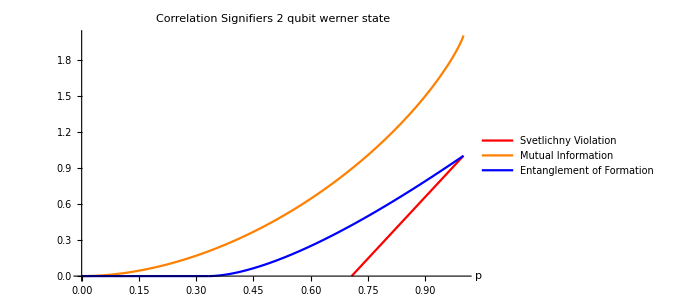

```mathematica
correlation=Show[svet,mi,eof,PlotLabel->"Correlation Signifiers 2 qubit werner state",LabelStyle->Directive[15, Black,FontFamily->"Times New Roman"]]
```

```mathematica
Export[SystemDialogInput["FileSave","correlation_signifiers_werner.png"],correlation,Background->None];
```